```mathematica
Grid[{{-Graphics-,"Anno Accademico 2017/18"}},ItemStyle->{Automatic,{1->{FontFamily->"Roboto Condensed",FontSize->20}}},Frame-> True,FrameStyle->{RGBColor[0.94,0.94,0.94]},Alignment->{{Left,Right}},Spacings->10,ItemSize-> Fit]
```

-Graphics- | Anno Accademico 2017/18

```mathematica
Grid[{{"Sistemi Lineari e Metodo di Gauss"}},ItemSize->Fit,Frame->True, FrameStyle->{RGBColor[0.13,0.52,0.96]},Spacings->{5,7},Background->{RGBColor[0.84,0.93,0.98]},ItemStyle->{Automatic, {1-> {FontFamily-> "Roboto Condensed", FontSize->40, FontColor->RGBColor[0.13,0.52,0.96]}}}]
```

Sistemi Lineari e Metodo di Gauss

```mathematica
Grid[{{-Graphics-, Column[{Style["Progetto D'Esame:", Red],"Matematica Computazionale (LM Informatica)\nCalcolo Numerico e Software Didattico (LM Matematica)","Sara Annese\nLaura Cappelli\nMatteo Del Vecchio\nMatteo Marchesini\nDaniele Rossi\nSilvia Scibilia"},Frame->None,Spacings->1]}}, ItemSize->Fit, Frame->None, Alignment->{{Right, Left}},Spacings->3, ItemStyle->{Automatic, {1-> {FontFamily->"Roboto Condensed", FontSize-> 18}}}]
```

-Graphics- | Progetto D'Esame:
Matematica Computazionale (LM Informatica)
Calcolo Numerico e Software Didattico (LM Matematica)
Sara Annese
Laura Cappelli
Matteo Del Vecchio
Matteo Marchesini
Daniele Rossi
Silvia Scibilia

```mathematica
forwardTag = "ReadySetGoTitle";
forwardButton := Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb",forwardTag}];
forwardLink := Hyperlink["Avanti", {"Home.nb", forwardTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvanti := Grid[{{forwardLink,forwardButton}},Alignment->{Right}, ItemSize->{{Scaled[0.93],Scaled[0.07]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvanti
Clear[forwardTag];
```

AvantiHome.nbReadySetGoTitleHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbReadySetGoTitleHome.nb

## Ready, Set, Go!

### 1. Clicca sul pulsante in basso per caricare il package necessario

```mathematica
loadPackageButton = Button[Style["Carica Package!", FontSize->30, RGBColor[0.13,0.52,0.96]],
	SetDirectory[NotebookDirectory[]]; Get["GaussLinearSystemsPackage.m"];
	MessageDialog["Il package è stato caricato correttamente!"]
];Grid[{{loadPackageButton}},ItemSize->Fit, Frame->True, FrameStyle->{RGBColor[0.94,0.94,0.94]}, Spacings->{40,0}]
```

Carica Package!

### 2. Valutazione delle celle

Mettere qui foto/gif/video di come fare la valutazione delle celle di inizializzazione

```mathematica
backTag = "Homepage";
forwardTag = "BlackboardHeader";
backButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb",backTag}];
backLink := Hyperlink["Indietro", {"Home.nb", backTag},BaseStyle->RGBColor[0.2,0.6,0.86]];

navAvantiIndietro := Grid[{{backButton,backLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.42],Scaled[0.42],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbHomepageHome.nb | IndietroHome.nbHomepageHome.nbHyperlinkHyperlinkActive | AvantiHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb

## Clicca su un argomento per iniziare...

```mathematica
buttonSistemi = Hyperlink[Button[-Graphics- , Background->White],{"Home.nb", "SistemiLineari"}];
buttonMatrici = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "MatriciPag1"}];
buttonGauss = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Gauss"}];
buttonEsercizi = Hyperlink[Button[-Graphics-, Background->White], {"Home.nb", "Esercizi"}];
SetDirectory[NotebookDirectory[]];
blackboard = Import["images/blackboardText.jpg"];
grid = Grid[{{buttonSistemi, buttonMatrici},{buttonGauss, buttonEsercizi}}];
Overlay[{blackboard,grid},All,2,Alignment->Center]
```

-Graphics--Graphics-Home.nbSistemiLineariHome.nb | -Graphics-Home.nbMatriciPag1Home.nb
-Graphics-Home.nbGaussHome.nb | -Graphics-Home.nbEserciziHome.nb

## Dai sistemi lineari...

## Nozioni fondamentali

```mathematica
firstPart = "Un sistema lineare è un sistema costituito da equazioni in cui le ";
styledPart = "incognite";
lastPart = " compaiono al primo grado.";
styledString = {firstPart, Style[styledPart, Red], lastPart};
styledString = Apply[StringJoin, ToString[#, StandardForm] & /@ styledString];
Grid[{{styledString}}, Frame->All, FrameStyle->RGBColor[1.0,0.0,0.0],ItemSize->Scaled[1],Spacings->{2,2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
```

Un sistema lineare è un sistema costituito da equazioni in cui le incognite compaiono al primo grado.

```mathematica
styledString2 = {"Le lettere x, y, z rappresentano le ", Style["incognite", Red], " del sistema.\nI termini a, b, c sono detti ", Style["coefficienti", RGBColor[0.13,0.52,0.96]], " e gli altri elementi sono chiamati ", Style["termini noti", RGBColor[0.14,0.61,0.14]]};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left]]
```

Le lettere x, y, z rappresentano le incognite del sistema.
I termini a, b, c sono detti coefficienti e gli altri elementi sono chiamati termini noti

```mathematica
(*Equations/:MakeBoxes[Equations[eqs_,Alignment->True],TraditionalForm]:=RowBox[{"{",MakeBoxes[#,TraditionalForm]&@Grid[{#1,"=",#2}&@@@{##}&@@eqs,Alignment->{{Right,Center,Left}}]}]*)

(*eqExample1= {Subscript[a,1]x+ Subscript[b,1]y+Subscript[c,1]z == Subscript[d,1], Subscript[a,2]x+ Subscript[b,2]y+Subscript[c,2]z ==  Subscript[d,2],
Subscript[a,3]x+ Subscript[b,3]y+Subscript[c,3]z == Subscript[d,3]};*)
(*eqExample1 = {Subscript[a,1]x+ Subscript[b,1]y+Subscript[c,1]z == Subscript[d,1]};*)

(*eqExample1 = {3x-5y==2, -8x+4y-2z==7}*)

(*highlightRules = <|x -> ToString[Style["x",Red], StandardForm],y -> ToString[Style["y",Red], StandardForm], z -> ToString[Style["z",Red], StandardForm],a -> ToString[Style["a",RGBColor[0.13,0.52,0.96]],StandardForm],b -> ToString[Style["b",RGBColor[0.13,0.52,0.96]],StandardForm], c -> ToString[Style["c",RGBColor[0.13,0.52,0.96]],StandardForm], d -> ToString[Style["d",RGBColor[0.14,0.61,0.14]],StandardForm] |>;
eqExample1 = eqExample1 /.highlightRules;*)

(*eqExample2 = eqExample2 /. highlightRules;*)

(*Grid[{{Equations[eqExample1,Alignment->True]//TraditionalForm,"ESEMPIO\n⟹" ,Equations[eqExample2,Alignment->True]//TraditionalForm}}, Frame->None, ItemSize->Fit, Spacings->{1,1}, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize -> 30, TextAlignment->Center]]*) 

formalSystem = {
Subscript[a, 1] x+Subscript[b, 1] y+Subscript[c, 1] z == Subscript[d, 1]//HoldForm//TraditionalForm,
Subscript[a, 2] x+Subscript[b, 2] y+Subscript[c, 2] z == Subscript[d, 2]//HoldForm//TraditionalForm,
Subscript[a, 3] x+Subscript[b, 3] y+Subscript[c, 3] z == Subscript[d, 3]//HoldForm//TraditionalForm
};
exampleSystem = {7x+ 6y - 5z ==  5, 3x - 4y + 2z ==  1, 5x + 6y+4z== 1};
Grid[{{displayEquationSystem[formalSystem],"ESEMPIO\n⟹" ,displayEquationSystem[exampleSystem]}}, Frame->None, ItemSize->Fit, Spacings->{1,1}, ItemStyle->Directive[FontFamily->"Roboto Condensed",FontSize -> 30, TextAlignment->Center]]
```

{a_1 x+b_1 y+c_1 z==d_1
a_2 x+b_2 y+c_2 z==d_2
a_3 x+b_3 y+c_3 z==d_3 | ESEMPIO
⟹ | {7 x+6 y-5 z==5
3 x-4 y+2 z==1
5 x+6 y+4 z==1

#### Attento! Le incognite sono x, y, z, le altre lettere che compaiono sono tutti numeri. Non confonderti!

```mathematica
forwardTag = "SistemiLineariPag2";
startButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb","BlackboardHeader"}];
startLink = Hyperlink["Torna all'Inizio", {"Home.nb", "BlackboardHeader"},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizio := Grid[{{startButton,startLink,forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.42],Scaled[0.42],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag2Home.nb

## Dai sistemi lineari...

## I sistemi di equazioni di primo grado: Esempio di un sistema di due equazioni in due incognite

#### Risolto per via grafica con metodo delle rette su piano cartesiano.

```mathematica
(*eqType1String = "Due equazioni in due incognite";
eqType2String = "Tre equazioni in tre incognite";
eqType3String = {Style["m", Bold], " equazioni in ", Style["n", Bold], " incognite (caso più generale)"};
eqType3String = Apply[StringJoin, ToString[#, StandardForm] & /@ eqType3String];*)

(*rulesIncognite = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;
rulesCoefficienti = <|2->Style["2", RGBColor[0.13,0.52,0.96]],3->Style["3", RGBColor[0.13,0.52,0.96]]|>;
rulesTerminiNoti = <|12->Style["12", RGBColor[0.14,0.61,0.14]],7->Style["7", RGBColor[0.14,0.61,0.14]]|>;*)
(*hightlightRules = <|x->Style["x", Red], y->Style["y", Red], z->Style["z", Red]|>;

eqsType1={Subscript[a,1] x + Subscript[b, 1] y == Subscript[c,1],Subscript[a,2] x + Subscript[b, 2] y == Subscript[c,2]};
eqsType1 = eqsType1 /. hightlightRules;

eqsType2 = {Subscript[a,1] x + Subscript[b, 1] y + Subscript[c,1] z == Subscript[d,1],Subscript[a,2] x + Subscript[b, 2] y + Subscript[c,2] z == Subscript[d,2], Subscript[a,3] x + Subscript[b, 3] y + Subscript[c,3] z == Subscript[d,3]};
eqsType2 = eqsType2 /. hightlightRules;

eqsType3 = {Subscript[a, 11] Subscript[x, "1"] + Subscript[a, 12] Subscript[x, "2"] + Subscript[a, HoldForm[1 n]] Subscript[x, "n"] == Subscript[b, 1],Subscript[a, 21] Subscript[x, "1"] + Subscript[a, 22] Subscript[x, "2"] + Subscript[a, HoldForm[2 n]] Subscript[x, "n"] == Subscript[b, 2],Subscript[a, 31] Subscript[x, "1"] + Subscript[a, 32] Subscript[x, "2"] + Subscript[a, HoldForm[3 n]] Subscript[x, "n"] == Subscript[b, 3],Subscript[a, HoldForm[m 1]] Subscript[x, "1"] + Subscript[a, HoldForm[m 2]] Subscript[x, "2"] + Subscript[a, HoldForm[m n]] Subscript[x, "n"] == Subscript[b, "m"]};
FullForm[eqsType3[[4]]]
eqsType3 = eqsType3 /. hightlightRules;

Grid[{{eqType1String, eqType2String, eqType3String},
{Equations[eqsType1, Alignment->True]//TraditionalForm, Equations[eqsType2, Alignment->True]//TraditionalForm, Equations[eqsType3, Alignment->True]//TraditionalForm}},
Frame->All, ItemSize->Fit, Spacings->{2,2}, ItemStyle->{FontFamily->"Roboto Condensed",{1->Directive[FontSize->20,FontName->"Arial"],2->Directive[FontSize->24]}}]*)
```

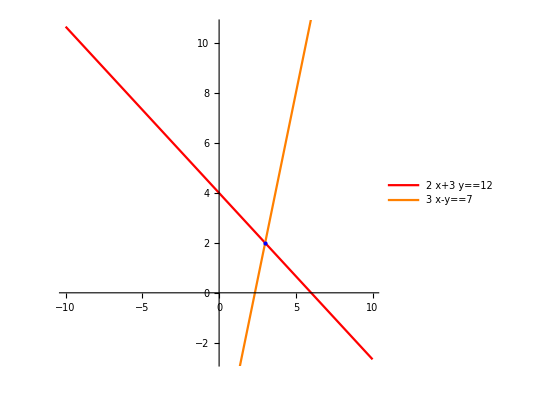
{2 x+3 y==12
3 x-y==7 | ⟹ |  | 2 | x | 3 | y | 12
3 | x | -1 | y | 7
-Graphics- |  |  |

```mathematica
(*rulesIncognite = <|x->Style[x, Red], y->Style[y, Red], z->Style[z, Red]|>;
rulesCoeffPag2 = <|2-> Style["2", RGBColor[0.13,0.52,0.96]],3->Style["3", RGBColor[0.13,0.52,0.96]]|>;
rulesTermPag2 = <|12->Style["12", RGBColor[0.14,0.61,0.14]],7->Style["7", RGBColor[0.14,0.61,0.14]]|>;*)

eqs2x2 = {2x+3y==12, 3x-y== 7};
(*eqs2x2Vis = eqs2x2 /. rulesIncognite /. rulesCoeffPag2 /. rulesTermPag2;*)

redLegend = {"Il colore ", Style["ROSSO", {Bold,Red}], " identifica le ", Style["INCOGNITE", Bold]};
redLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ redLegend];

blueLegend = {"Il colore ", Style["BLU", {Bold,Blue}], " identifica i ", Style["COEFFICIENTI", Bold]};
blueLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ blueLegend];

greenLegend = {"Il colore ", Style["VERDE", {Bold,RGBColor[0.14,0.61,0.14]}], " identifica i ", Style["TERMINI NOTI", Bold]};
greenLegendString = Apply[StringJoin, ToString[#,StandardForm]& /@ greenLegend];

legend=SwatchLegend[{Red,RGBColor[0.13,0.52,0.96],RGBColor[0.14,0.61,0.14]},{redLegendString,blueLegendString,greenLegendString}];

Grid[{{displayEquationSystem[eqs2x2],"⟹",SpanFromLeft,highlightElementsTable[eqs2x2]},{plotLinearSystem2[eqs2x2[[1]],eqs2x2[[2]]],SpanFromLeft,legend,SpanFromLeft}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.45],Scaled[0.05],Scaled[0.05],Scaled[0.45]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40,FontSize->20},{1,3}->{Alignment->Left}}]
```

```mathematica
backTag = "SistemiLineari";
forwardTag = "SistemiLineariPag3";
navAvantiInizioIndietro := Grid[{{backButton, backLink, startButton, startLink, forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Left, Right, Right}}, ItemSize->{{Scaled[0.08],Scaled[0.25], Scaled[0.08],Scaled[0.25],Scaled[0.25],Scaled[0.08]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariHome.nb | IndietroHome.nbSistemiLineariHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbSistemiLineariPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbSistemiLineariPag3Home.nb

## Dai sistemi lineari...

## I sistemi di equazioni di primo grado: Esempio di sistema di tre equazioni in tre incognite

```mathematica
(*rulesCoeffPag3 = <|2:>(Style["2", RGBColor[0.13,0.52,0.96]]//TraditionalForm),-3:> (Style["-3", RGBColor[0.13,0.52,0.96]]//TraditionalForm)|>;
rulesTermPag3 = <|6:> Style["6", RGBColor[0.14,0.61,0.14]],1:> Style["1", RGBColor[0.14,0.61,0.14]]|>;

rulesRewrite = <|6->"6tn", 1->"1tn", -1->"-1tn"|>;*)

(*eqs3x3Vis = eqs3x3 /. rulesIncognite /. rulesCoeffPag3;
eqs3x3 // FullForm;
eqs3x3 /. rulesIncognite // FullForm;
eqs3x3 /. rulesIncognite /. rulesCoeffPag3 // FullForm;
eqs3x3 /. rulesIncognite /. rulesCoeffPag3 /. rulesTermPag3
eqs3x3 /. {rulesIncognite, rulesCoeffPag3, rulesTermPag3};*)

(*eqs3x3Replaced = eqs3x3 /. rulesRewrite;
result = Level[eqs3x3[[2]], 1];
Level[%[[1]],1];
lhs = Level[eqs3x3[[3]],1][[2]];
variabili = Variables[lhs];
(*CoefficientList[lhs,y]*)
CoefficientRules[lhs,variabili];
Values[%];

For[i=1,i≤Length[eqs3x3],i++,
	(*Print[eqs3x3[[i]]];*)
	termineNoto = Level[eqs3x3[[i]],1][[2]];
	lhs = Level[eqs3x3[[i]],1][[1]];
	variabili = Sort[Variables[lhs]];
	coefRules = CoefficientRules[lhs,variabili];
	Print[coefRules];
	Print[FromCoefficientRules[coefRules, variabili]];
	coefficienti = Values[coefRules];
	For[j=1,j≤Length[coefficienti],j++,coefficienti[[j]] = Style[coefficienti[[j]],RGBColor[0.13,0.52,0.96]]];
	For[j=1,j≤Length[variabili],j++,variabili[[j]] = Style[variabili[[j]],RGBColor[1.0,0,0]]];
	termineNoto = Style[termineNoto, RGBColor[0.14,0.61,0.14]];
	flattened = Flatten[{coefficienti,variabili,termineNoto}];
	Print[flattened];
]*)
eqs3x3 = {x+y+z==6,2x+y-z==1,2x-3y+z==-1};
Grid[{{displayEquationSystem[eqs3x3],"⟹",SpanFromLeft,highlightElementsTable[eqs3x3]},{plotLinearSystem3[eqs3x3[[1]],eqs3x3[[2]],eqs3x3[[3]]], SpanFromLeft,legend,SpanFromLeft}},Frame->All,FrameStyle->RGBColor[0.94,0.94,0.94],Spacings->{5,5},ItemSize->{{Scaled[0.45],Scaled[0.05],Scaled[0.05],Scaled[0.45]}},Alignment->Center,ItemStyle->{FontFamily->"Roboto Condensed",{FontSize->40,FontSize->20},{1,3}->{Alignment->Left}}]
```

{x+y+z==6
2 x+y-z==1
2 x-3 y+z==-1 | ⟹ |  | 1 | x | 1 | y | 1 | z | 6
2 | x | 1 | y | -1 | z | 1
2 | x | -3 | y | 1 | z | -1
-Graphics3D- |  |  |

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb","BlackboardHeader"}];
forwardButton = Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb","Risoluzione"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}];*)

backTag = "SistemiLineariPag2";
forwardTag = "Risoluzione";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbSistemiLineariPag2Home.nb | IndietroHome.nbSistemiLineariPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbRisoluzioneHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbRisoluzioneHome.nb

## Dai sistemi lineari...

## Risoluzione

```mathematica
myString1= "Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.\nProsegui al ";

nextChapterButton = Hyperlink[Button[Style["prossimo capitolo", FontFamily-> "Roboto Condensed", FontSize-> 24, RGBColor[0.13,0.52,0.96], Bold], Appearance-> {None}],{"Home.nb", "BlackboardHeader"}];
myString2 =" per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.\nÈ un metodo generale che, come vedremo, include casi particolari come quelli che già conosci";
myString3 = {myString1,nextChapterButton,myString2};
myString3 = Apply[StringJoin, ToString[#, StandardForm]& /@ myString3];
Grid[{{myString3}}, Frame -> None, Alignment->{{Left, Right}},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Left] ]
```

Dovresti già conoscere qualche metodo per risolvere i sistemi lineari.
Prosegui al prossimo capitolo per scoprire un nuovo strumento per trovare la soluzione di sistemi lineari.
È un metodo generale che, come vedremo, include casi particolari come quelli che già conosci

```mathematica
navInizio := Grid[{{startButton,startLink}},Alignment->{Left}, ItemSize->{{Scaled[0.07],Scaled[0.93]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navInizio
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive

## ... alle Matrici

```mathematica
styledString2 ={"È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono: i coefficienti e i termini noti del sistema.\nQuesta è detta ", Style["MATRICE COMPLETA", Red], ". ", Style["I coefficienti devono essere ordinati.", Underlined],"\n\nGuarda i colori per comprendere il posizionamento dei numeri"};
styledString2 = Apply[StringJoin, ToString[#, StandardForm]& /@styledString2];
Grid[{{styledString2}}, Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]

linearSystem1 = {7x+6y+5z==-5, 3x-4y+2z==1, -5x+6y-4z == 1};
matrixForm1= highlightMatrixElements[transformToMatrix[linearSystem1,True]]//MatrixForm;

linearSystem2= {7x+6y+5z==0,-4y+2z ==1,5x+6y==1};
matrixForm2 = highlightMatrixElements[transformToMatrix[linearSystem2,True]]//MatrixForm;

Grid[{{displayEquationSystem[linearSystem1],"⟹",matrixForm1},{displayEquationSystem[linearSystem2],"⟹",matrixForm2}},Frame -> None, ItemSize->Fit, Spacings->{1, 2}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
Spacer[20]
```

È possibile rappresentare un sistema lineare come una matrice, ossia una tabella ordinata i cui elementi sono: i coefficienti e i termini noti del sistema.
Questa è detta MATRICE COMPLETA. I coefficienti devono essere ordinati.

Guarda i colori per comprendere il posizionamento dei numeri

{7 x+6 y+5 z==-5
3 x-4 y+2 z==1
-5 x+6 y-4 z==1 | ⟹ | (7 | 6 | 5 | -5
3 | -4 | 2 | 1
-5 | 6 | -4 | 1)
{7 x+6 y+5 z==0
-4 y+2 z==1
5 x+6 y==1 | ⟹ | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 6 | 0 | 1)

#### Attenzione ! Se nel sistema non compare un’incognita, nella matrice al posto corrispondente bisogna mettere uno 0 (zero).

```mathematica
(*exerciseButton = Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb", "BlackboardHeader"}];
forwardButton = Hyperlink[Button[-Graphics-, ImageSize->{80,80}, Appearance->{None}],{"Home.nb","MatriciPag2"}];Grid[{{exerciseButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}];*)

forwardTag = "MatriciPag2";
navAvantiInizio
Clear[forwardTag];
```

-Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag2Home.nb

## Matrici

## Definizione informale di matrice

```mathematica
matrixRule = <| "1"-> Style[matrix[[1,1,1,2,1]], RGBColor[0.13,0.52,0.96]], 1-> Style[matrix[[1,1,1,2,1]], Red], 2 -> Style[matrix[[1,2,1,2,1]], Red], "2" -> Style[matrix[[1,2,1,2,1]],RGBColor[0.13,0.52,0.96]], "m" -> Style[matrix[[1,1,4,2,1,2]], Red], "n" -> Style[matrix[[1,4,1,2,1]], RGBColor[0.13,0.52,0.96]]|>;
matrixElementRule = <| "i" ->  Style[matrixElement[[2,1,1]], RGBColor[0.13,0.52,0.96]], "j" -> Style[matrixElement[[2,1,2]], Red]|>;
matrix ={{Subscript[a, HoldForm["1"1]], Subscript[a, HoldForm["1"2]], …, Subscript[a, HoldForm["1""m"]]}, {Subscript[a, HoldForm["2"1]], Subscript[a, HoldForm["2"2]], …, Subscript[a, HoldForm["2""m"]]}, {⋮, ⋮, ⋱, ⋮}, {Subscript[a, HoldForm["n"1]], Subscript[a, HoldForm["n"2]], …, Subscript[a, HoldForm["n""m"]]}} // MatrixForm;
matrixElement = Subscript[a, HoldForm["i""j"]];
myMatrix = matrix /. matrixRule;
myMatrixElement = matrixElement /. matrixElementRule;
stringMatrix = {"matrice ", Style["n", RGBColor[0.13,0.52,0.96]], " x ",  Style["m", Red]};
stringMatrix = Apply[StringJoin, ToString[#, StandardForm]& /@ stringMatrix];
columns= -Graphics-;
rows = -Graphics-;
(*Grid[{{"Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne."},{Framed[Grid[{{Framed[myMatrixElement, FrameMargins-> {{20,0}, {0, 0}},FrameStyle -> None], columns}, {rows, myMatrix}, {Framed[stringMatrix, FrameMargins-> {{85,0}, {0, 0}},FrameStyle -> None], SpanFromLeft }}, Frame -> None, ItemStyle ->Directive[FontFamily->"Roboto Condensed",FontSize -> 30]], FrameMargins-> {{0,0}, {0,30}}, FrameStyle-> None]}}, ItemSize->Fit]*)

Grid[{{"Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne."},{
Grid[{{myMatrixElement,columns},{rows,myMatrix},{stringMatrix,SpanFromLeft}},Frame->None]
}}, ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28], ItemSize->Fit, Frame->None]

Spacer[20]

Grid[{{"Al suo interno possono comparire numeri positivi, negativi o anche zeri."}},Frame -> None, ItemSize->Scaled[1], Spacings->{2, 2},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->28, TextAlignment->Center]]
```

Una matrice è una tabella ordinata di elementi disposti su n righe e m colonne.
a_(i j) | -Graphics-
-Graphics- | (a_(1 1) | a_(1 2) | … | a_(1 m)
a_(2 1) | a_(2 2) | … | a_(2 m)
⋮ | ⋮ | ⋱ | ⋮
a_(n 1) | a_(n 2) | … | a_(n m))
matrice n x m |

Al suo interno possono comparire numeri positivi, negativi o anche zeri.

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag1"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag3"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag1";
forwardTag = "MatriciPag3";
exerciseTag = "TAGQUI";
exerciseButton := Hyperlink[Button[-Graphics-, Appearance->{None}, ImageSize->{80,80}],{"Home.nb", exerciseTag}];
exerciseLink := Hyperlink["Prova tu!", {"Home.nb", exerciseTag},BaseStyle->RGBColor[0.2,0.6,0.86]];
navAvantiInizioEserciziIndietro := Grid[{{backButton, backLink, startButton, startLink, exerciseButton, exerciseLink, forwardLink,forwardButton}},Alignment->{{Left, Left, Right, Left, Right, Left, Right, Right}}, ItemSize->{{Scaled[0.09],Scaled[0.15], Scaled[0.09],Scaled[0.22],Scaled[0.09],Scaled[0.15],Scaled[0.1],Scaled[0.09]}}, Frame->All, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{3,6},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->30, FontWeight->Bold]];
navAvantiInizioEserciziIndietro
Clear[backTag, forwardTag,exerciseTag];
```

-Graphics-Home.nbMatriciPag1Home.nb | IndietroHome.nbMatriciPag1Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | -Graphics-Home.nbTAGQUIHome.nb | Prova tu!Home.nbTAGQUIHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag3Home.nb

## Matrici

## Elemento di una matrice

```mathematica
matrixPhrase="Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.";

tableMatrix =Grid[
Table[
{
{"", Rotate[" 1.aa Colonna", Pi/2],Rotate[" 2.aa Colonna", Pi/2],Rotate[" 3.aa Colonna", Pi/2],Rotate[" 4.aa Colonna", Pi/2]},
{"1.aa riga",7,6,5,0},
{"2.aa riga",0,-4,2,1},
{"3.aa riga",5,Item[7, Frame-> True, FrameStyle->Directive[Yellow, Thickness-> Large]],0,1}}
],
Dividers->{{None,Black,None,None,None,Black},{None, Black, None, None, Black}}, Background->{Automatic,Automatic,{{{4,4},{2,5}}->Red,{{2,4},{3,3}}->Blue}}, ItemStyle->{Automatic,Automatic,{{2,4},{3,3}}->{FontColor->White}}];
exampleImage = -Graphics-;
Grid[{{matrixPhrase},{tableMatrix}, {exampleImage}}, Frame -> None, ItemSize->Scaled[1], Spacings->{3, 3},ItemStyle->Directive[FontFamily->"Roboto Condensed", FontSize->24, TextAlignment->Center]]
```

Un elemento è individuato univocamente da due indici ordinati: il numero di riga e il numero di colonna.
 |  1.aa Colonna |  2.aa Colonna |  3.aa Colonna |  4.aa Colonna
1.aa riga | 7 | 6 | 5 | 0
2.aa riga | 0 | -4 | 2 | 1
3.aa riga | 5 | 7 | 0 | 1
-Graphics-

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag2"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag4"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag2";
forwardTag = "MatriciPag4";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag2Home.nb | IndietroHome.nbMatriciPag2Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag4Home.nb

## Matrici

## Sottotitolo da aggiungere QUI

```mathematica
firstStringSquaredMatrix = {Style["Matrice quadrata\n", Bold], "numero di righe = numero di colonne"};
firstStringSquaredMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringSquaredMatrix];
firstStringRectangularMatrix = {Style["Matrice rettangolare\n", Bold], Style["numero di righe ≠ numero di colonne", FontFamily-> "Roboto Condensed", FontSize-> 24]};
firstStringRectangularMatrix = Apply[StringJoin, ToString[#, StandardForm] & /@ firstStringRectangularMatrix];
squaredMatrix = {{7, 6, 5}, {0, -4, 2}, {5, 7, 0}} // MatrixForm;
rectangularMatrix = {{7, 6, 5, 0}, {0, -4, 2, 1}, {5, 7, 0, 1}} // MatrixForm;
secondStringSquaredMatrix = Style["Matrice 3 x 3", Italic];
secondStringRectangularMatrix = Style["Matrice 3 x 4", Italic];

Grid[{{firstStringSquaredMatrix,firstStringRectangularMatrix}, {squaredMatrix, rectangularMatrix}, {secondStringSquaredMatrix, secondStringRectangularMatrix}}, Frame-> None, Spacings-> {1,1}, ItemSize-> Fit ,ItemStyle-> Directive[TextAlignment -> Center, FontFamily -> "Roboto Condensed", FontSize -> 24]]
```

Matrice quadrata
numero di righe = numero di colonne | Matrice rettangolare
numero di righe ≠ numero di colonne
(7 | 6 | 5
0 | -4 | 2
5 | 7 | 0) | (7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 0 | 1)
Matrice 3 x 3 | Matrice 3 x 4

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag3"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag5"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag3";
forwardTag = "MatriciPag5";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag3Home.nb | IndietroHome.nbMatriciPag3Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag5Home.nb

## Matrici

## Diagonale di una matrice

```mathematica
firstString = "La diagonale di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.\nSono quelli evidenziati in rosso.";
secondString = {Style["Attenzione!\n", Red, Bold], "Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {5, 7, Style[0, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {5, 7, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

Grid[{{firstString}, {squaredMatrix}, {secondString}, {rectangularMatrix}}, Frame -> None, Spacings-> {0,2}, ItemSize-> Fit, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

La diagonale di una matrice quadrata è composta dai numeri che hanno indice di riga uguale a indice di colonna.
Sono quelli evidenziati in rosso.
(7 | 6 | 5
0 | -4 | 2
5 | 7 | 0)
Attenzione!
Non esiste la diagonale di una matrice rettangolare, tuttavia nelle matrici complete che tratteremo ci sarà utile un concetto simile per riconoscere elementi particolari.
(7 | 6 | 5 | 0
0 | -4 | 2 | 1
5 | 7 | 3 | 1)

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag4"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag6"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag4";
forwardTag = "MatriciPag6";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag4Home.nb | IndietroHome.nbMatriciPag4Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag6Home.nb

## Matrici

## Matrice triangolare e a gradini

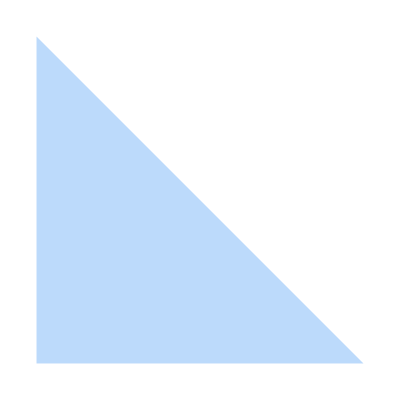
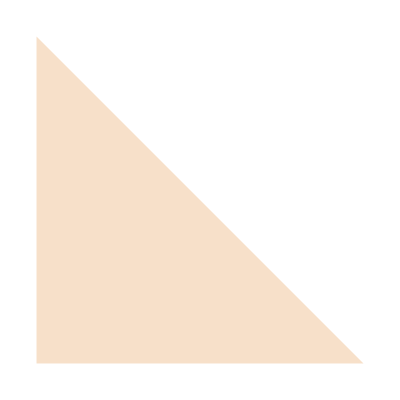
Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di matrice triangolare superiore.
-Graphics-(7 | 6 | 5
0 | -4 | 2
0 | 0 | 9)
Una matrice rettangolare a gradini presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo pivot.
-Graphics-(7 | 6 | 5 | 0
0 | -4 | 2 | 1
0 | 0 | 3 | 1)

```mathematica
firstString = {"Una matrice quadrata che presenta tutti elementi uguali a zero sotto la diagonale prende il nome di ", Style["matrice triangolare superiore", Bold], "."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"Una ", Style["matrice rettangolare a gradini", Bold], " presenta tutti elementi uguali a zero sotto i numeri evidenziati in verde che chiameremo ", Style["pivot",  RGBColor[0.2, 0.6, 0.2], Bold], "."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

squaredMatrix = {{Style[7, Red], 6, 5}, {0, Style[-4, Red], 2}, {0, 0, Style[9, Red]}}  // MatrixForm;
rectangularMatrix = {{Style[7, RGBColor[0.2, 0.6, 0.2]], 6, 5, 0}, {0, Style[-4, RGBColor[0.2, 0.6, 0.2]], 2, 1}, {0, 0, Style[3, RGBColor[0.2, 0.6, 0.2]], 1}} // MatrixForm;

triangle = Triangle[{{0,0}, {0,1}, {1,0}}];
triangleGridSquaredMatrix = Grid[{{Graphics[{RGBColor[0.13,0.52,0.96, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
triangleGridRectagularMatrix = Grid[{{Graphics[{RGBColor[0.9,0.60,0.30, 0.3], triangle}]}}, ItemSize-> 4.5, Frame -> True,FrameStyle -> RGBColor[0.94,0.94,0.94], Spacings -> {0.5,1}];
upperTriangularMatrix = Overlay[{triangleGridSquaredMatrix, squaredMatrix},All, 2];
rectangularSteppedMatrix = Overlay[{triangleGridRectagularMatrix, rectangularMatrix},All, 2];

Grid[{{firstString}, {upperTriangularMatrix}, {secondString}, {rectangularSteppedMatrix}}, Frame -> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag5"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag7"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag5";
forwardTag = "MatriciPag7";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag5Home.nb | IndietroHome.nbMatriciPag5Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag7Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag7Home.nb

## Matrici

## Matrice diagonale e matrice identità

```mathematica
firstString = {"Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama ", Style["matrice diagonale", Bold],"."};
firstString= Apply[StringJoin, ToString[#, StandardForm] & /@ firstString];
secondString = {"La matrice diagonale che presenta solo 1 sulla diagonale si chiama ", Style["matrice identità", Bold],"."};
secondString = Apply[StringJoin, ToString[#, StandardForm] & /@ secondString];

diagonalMatrix = {{Style[7, Red], 0, 0}, {0, Style[-4, Red], 0}, {0, 0, Style[9, Red]}} // MatrixForm;
identityMatrix = {{Style[1, Red], 0, 0}, {0, Style[1, Red], 0}, {0, 0, Style[1, Red]}} // MatrixForm;

Grid[{{firstString}, {diagonalMatrix}, {secondString}, {identityMatrix}}, Frame-> None, ItemSize-> Fit, Spacings-> {0,2}, ItemStyle-> Directive[FontFamily -> "Roboto Condensed", FontSize -> 24, TextAlignment -> Center]]
```

Una matrice quadrata che presenta elementi diversi da zero solo sulla diagonale si chiama matrice diagonale.
(7 | 0 | 0
0 | -4 | 0
0 | 0 | 9)
La matrice diagonale che presenta solo 1 sulla diagonale si chiama matrice identità.
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*backButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize -> {80,80}], {"Home.nb", "MatriciPag6"}];
forwardButton = Hyperlink[Button[-Graphics-, Appearance-> {None}, ImageSize-> {80,80}], {"Home.nb", "MatriciPag8"}];
Grid[{{backButton,forwardButton}},Alignment->{{Left, Right}}, ItemSize->Fit, Frame->True, FrameStyle->RGBColor[0.94,0.94,0.94], Spacings->{10,3}]*)
backTag = "MatriciPag6";
forwardTag = "MatriciPag8";
navAvantiInizioIndietro
Clear[backTag,forwardTag];
```

-Graphics-Home.nbMatriciPag6Home.nb | IndietroHome.nbMatriciPag6Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbBlackboardHeaderHome.nb | Torna all'InizioHome.nbBlackboardHeaderHome.nbHyperlinkHyperlinkActive | AvantiHome.nbMatriciPag8Home.nbHyperlinkHyperlinkActive | -Graphics-Home.nbMatriciPag8Home.nb

```mathematica
sistemaProva = getRandomSystem[];
displayEquationSystem[sistemaProva]
matrix = transformToMatrix[sistemaProva,True];
dims = calculateMatrixDims[sistemaProva]
highlightMatrixElements[transformToMatrix[sistemaProva,True]]//MatrixForm
inputMatrix = ConstantArray[0,dims[[1]]*dims[[2]]];
m = Partition[Table[With[{i=i},InputField[Dynamic[inputMatrix[[i]]],FieldSize->{1,1}]],{i,dims[[1]]*dims[[2]]}],dims[[2]]];
Style[MatrixForm[m],Large]
reshaped = ArrayReshape[inputMatrix,dims]
Dynamic[inputMatrix]
Dynamic[ArrayReshape[inputMatrix,dims]]
Dynamic[MatchQ[matrix,ArrayReshape[inputMatrix,dims]]]
```

{x+y-z==6
x+y==3
x+z==0

{3,4}

(1 | 1 | -1 | 6
1 | 1 | 0 | 3
1 | 0 | 1 | 0)

( |  |  | 
 |  |  | 
 |  |  | )

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
exerciseSystemToMatrix[]
```

{2 x-y==0
x+3 y==1 | ( |  | 
 |  | ) | Verifica!